## 6강 다변수 함수

전경원 <ruddyscent@gmail.com>

2014년 11월 3일 월요일

```mathematica
$Version
DateString[]
```

10.0 for Linux x86 (64-bit) (September 9, 2014)

Mon 3 Nov 2014 17:57:10

## 벡터

매스매티카에서 2차원 벡터는 원소 2개의 리스트로 표현합니다.

```mathematica
{2,5}+{17,-4}
```

{19,1}

```mathematica
-4{2,5}
```

{-8,-20}

```mathematica
i={1,0};
j={0,1};
2i+5j
```

{2,5}

3차원 벡터는 원소 3개짜리 벡터로 나타나겠죠.

```mathematica
{3,-57,8}+{57,-3,π/4}
```

{60,-60,8+π/4}

### 백터의 내적과 크기

내적은 "."으로 표현합니다.

```mathematica
{Subscript[u, 1],Subscript[u, 2]}.{Subscript[v, 1],Subscript[v, 2]}
```

u_1 v_1+u_2 v_2

```mathematica
{3,4}.{4,5}
```

32

벡터의 크기는 Norm 명령으로 계산할 수 있습니다.

```mathematica
Norm[{3,4}]
```

5

```mathematica
Norm[{Subscript[u, 1],Subscript[u, 2]}]
```

√(Abs[u_1]^2+Abs[u_2]^2)

두 벡터의 사잇각은 아래와 같이 구할 수 있습니다.

```mathematica
u={2,4};
v={9,-13};
ArcCos[(u.v)/(Norm[u]Norm[v])]//N
%/Degree HoldForm[°]
```

2.0724

118.74 °

### 벡터 그리기

벡터는 화살표를 이용하여 그려볼 수 있습니다.

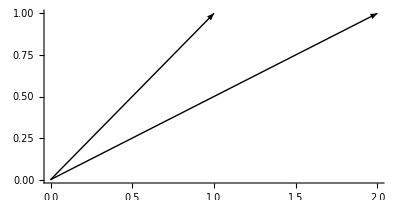

```mathematica
Graphics[{Arrow@{{0,0},{1,1}},Arrow@{{0,0},{2,1}}},Axes->True]
```

벡터 합을 그래프로 표현해 볼께요.

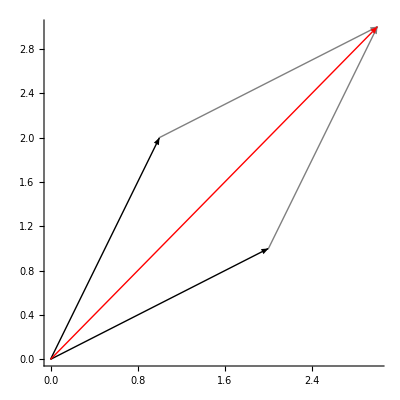

```mathematica
Clear[u,v]
u={1,2};
v={2,1};
Graphics[{
Arrow[{{0,0},u}],Arrow[{{0,0},v}],
{Gray,Arrow[{u,u+v}],Arrow[{v,u+v}]},
{Red,Arrow[{{0,0},u+v}]}
},Axes->True]
Clear[u,v]
```

다음은 역동적으로

```mathematica
Manipulate[Graphics[{
Arrow[{{0,0},u}],Arrow[{{0,0},v}],
{Gray,Arrow[{u,u+v}],Arrow[{v,u+v}]},
{Red,Arrow[{{0,0},u+v}]}
},PlotRange->3,Axes->True],
{{u,{1,2}},Locator,Appearance->None},
{{v,{2,1}},Locator,Appearance->None}]
```

### 벡터의 외적

매스매티카로 외적 공식을 구해보죠.

```mathematica
Clear[u,v]
Cross[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]}]
```

{-u_3 v_2+u_2 v_3,u_3 v_1-u_1 v_3,-u_2 v_1+u_1 v_2}

외적의 값을 구할 수도 있어요.

```mathematica
Cross[{1,3,5},{7,9,11}]
```

{-12,24,-12}

부호로는 "×"로 나타낼 수 있어요.

```mathematica
{1,3,5}×{7,9,11}
```

{-12,24,-12}

## 다변수 함수

변수가 두 개 이상인 함수도 쉽게 정의할 수 있습니다.

```mathematica
Clear[f]
f[x_,y_]:=Sin[x^2-y^2]
```

변수에 숫자를 넣으면 함수의 값을 얻을 수 있지요.

```mathematica
f[0,√(π/4)]
```

-1/(√2)

결과가 복잡하다면, Simplify로 간단하게 정리할 수 있습니다.

```mathematica
f[1-π,1+π]
%//Simplify
```

Sin[(1-π)^2-(1+π)^2]

0

### 다변수 함수의 그래프

변수가 두 개인 함수의 그래프는 Plot3D 명령으로 그립니다.

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-1,1}]
```

-Graphics3D-

3차원 그래프가 멋있긴 하지만, 때론 단면을 보는 게 더 정확한 분석을 하는데 도움을 주기도 합니다.

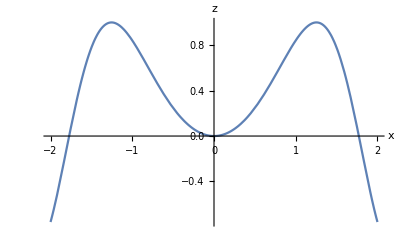

```mathematica
Plot[f[x,0],{x,-2,2},AxesLabel->{x,z}]
```

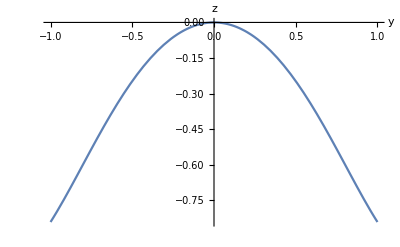

```mathematica
Plot[f[0,y],{y,-1,1},AxesLabel->{y,z}]
```

## 다른 좌표계

### 극 좌표계

#### 극 좌표계로 그리고, 극 좌표계로부터

극 좌표계에서 좌표는 두 개의 숫자 쌍(r,θ)으로 표현합니다. r은 원점으로부터의 거리이고, θ는 양의 x축으로부터 반시계방향으로 잰 각을 라디안으로 나타낸 값입니다.

```mathematica
CoordinateTransform["Cartesian"->"Polar",{-1,√3}]
```

{2,(2 π)/3}

```mathematica
CoordinateTransform["Polar"->"Cartesian",{10,π/12}]
```

{(5 (1+√3))/(√2),(5 (-1+√3))/(√2)}

#### 극 좌표계의 그래프

극 좌표계에서 정의된 함수, r=f(θ)의 그래프를 그릴 땐, PolarPlot을 이용합니다.

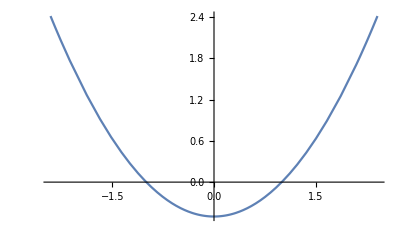

```mathematica
PolarPlot[1/(1-Sin[θ]),{θ,(-5π)/4,π/4}]
```

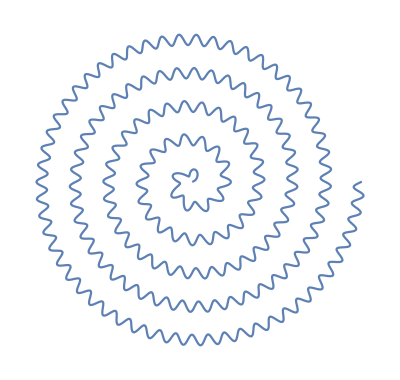

```mathematica
PolarPlot[θ+Sin[θ^2],{θ,0,10π},Axes->False]
```

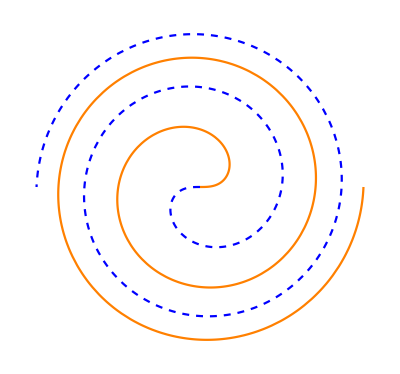

```mathematica
PolarPlot[{√θ,-√θ},{θ,0,4π},Axes->False,PlotStyle->{Orange,Directive[Blue,Dashed]}]
```